-Graphics-

Calculation Notebook

Students

Surname1, Name1, Student-ID, xxx.xxx@xxx.de

Surname2, Name2, Student-ID, xxx.xxx@xxx.de

Surname3, Name3, Student-ID, xxx.xxx@xxx.de

Lecture		Optimization and Data Analytics

Lecturer		Prof. Dr. Frank Brand

## Content Overview

Statutory Declaration

1 Executive Summary     xx

2 Intoduction     xx

3 Problem Statement     xx

4 Solution     xx

4.1 xxx     xx

4.2 xxx     xx

4.3 xxx     xx

5 Sensitivity Analysis     xx

5.1 xxx     xx

5.2 xxx     xx

5.3 xxx     xx

6 Possible Generalizations of the Problem     xx

6.1 xxx     xx

6.2 xxx     xx

6.3 xxx     xx

7 Consequenses and Recommendations     xx

8 Summary of results     xx

## Statutory Declaration

I hereby formally declare that we have written the submitted term peper entirely by ourselfes without anyone else’s assistance. Wherever we have drawn on literature or other sources, either in direct quotes or in paraphrasing such material, we have given the reference to the original author or authors and to the source where it appeared. We are aware that the use of quotations, or close paraphrasing, from books, magazines, newspapers, the internet, or other sources, which are not marked as such, will be considered an attempt at deception, and that the term paper will be graded with a fail. We are aware of the fact, that the use of Large Language Models (LLM) like ChatGPT or others without a quotation will be graded with a fail, too.

____________________

Location / Date

___________________________

Signature

___________________________

Signature

___________________________

Signature

## 1 Setup

```mathematica
maxdimension = 7;
```

```mathematica
F[n_]:=Sum[IntegerDigits[n][[i]]^IntegerLength[n],{i,1,IntegerLength[n]}]
```

```mathematica
QF[n_]:=(n-Sum[IntegerDigits[n][[i]]^IntegerLength[n],{i,1,IntegerLength[n]}])^2
```

```mathematica
QF[153]
QF[152]
```

0

324

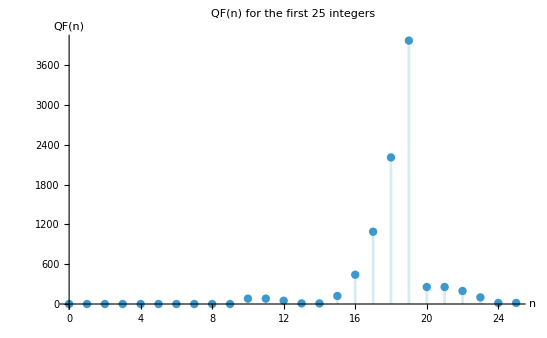

```mathematica
Plot1 = Show[DiscretePlot[QF[n],{n,0,25},AxesLabel->{"n","QF(n)"},PlotLabel->"QF(n) for the first 25 integers"],PlotRange->Full]
```

```mathematica
returnNarcissisticRange[lower_,upper_]:=Module[{time,numbers},{time,numbers}=AbsoluteTiming[Select[Range[lower,upper],QF[#]==0&]];
{numbers,time}]
```

## 2 Brute Force

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticRange[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Table1 = Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

Upper bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.000045
10^1 | ; ; 23456789 | 0.000055
10^2 | ; ;  | 0.000601
10^3 | ; ; 153370371407 | 0.007222
10^4 | ; ; 163482089474 | 0.085989
10^5 | ; ; 547489272793084 | 1.035760
10^6 | ; ; 548834 | 11.275136
10^7 | ; ; 1741725421081898008179926315 | 124.984849

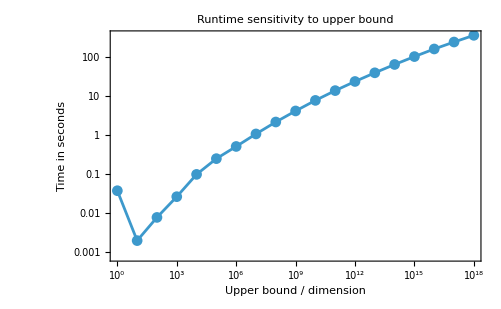

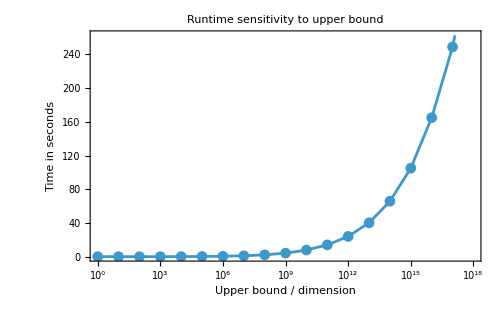

```mathematica
plotData=rows/. {Superscript[10,k_],numbers_,NumberForm[time_,___]}:>{k,time};
Plot2=ListLogPlot[plotData,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / dimension","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData),None}},PlotLabel->"Runtime sensitivity to upper bound"]
Plot2NonLog = ListPlot[plotData,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / dimension","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData),None}},PlotLabel->"Runtime sensitivity to upper bound"]
```

```mathematica
Clear[dimensionRange]

dimensionRange[d_Integer]:=If[d==1,{0,9},{10^(d-1),10^d-1}]

maxdimensionParallelBF=8;
```

```mathematica
Clear[returnNarcissisticParallelRange]

returnNarcissisticParallelRange[lower_Integer,upper_Integer]:=Module[{time,numbers},If[$KernelCount==0,LaunchKernels[]];
DistributeDefinitions[F,QF];
{time,numbers}=AbsoluteTiming[ParallelTable[If[QF[i]==0,i,Nothing],{i,lower,upper},Method->"CoarsestGrained"]];
{numbers,time}]
```

```mathematica
rows=Table[Module[{lower,upper,numbers,time},{lower,upper}=dimensionRange[d];
{numbers,time}=returnNarcissisticParallelRange[lower,upper];
{d,Row[{lower," - ",upper}],Row[numbers,"; "],NumberForm[time,{Infinity,3}]}],{d,1,maxdimensionParallelBF}];

Table2 = Grid[Prepend[rows,{"Digit length","Search range","Numbers","Time in seconds"}],Frame->All]
```

Digit length | Search range | Numbers | Time in seconds
1 | 0 - 9 | ; ; 0123456789 | 0.032
2 | 10 - 99 | ; ;  | 0.004
3 | 100 - 999 | ; ; 153370371407 | 0.041
4 | 1000 - 9999 | ; ; 163482089474 | 0.046
5 | 10000 - 99999 | ; ; 547489272793084 | 0.236
6 | 100000 - 999999 | ; ; 548834 | 2.353
7 | 1000000 - 9999999 | ; ; 1741725421081898008179926315 | 28.573
8 | 10000000 - 99999999 | ; ; 246780502467805188593477 | 331.815

```mathematica
CloseKernels[]
```

{Local,Local,Local,Local,Local,Local}

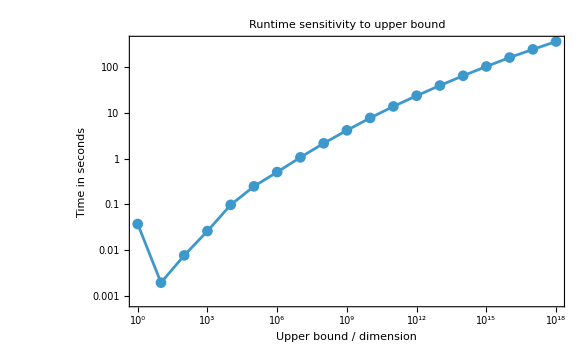

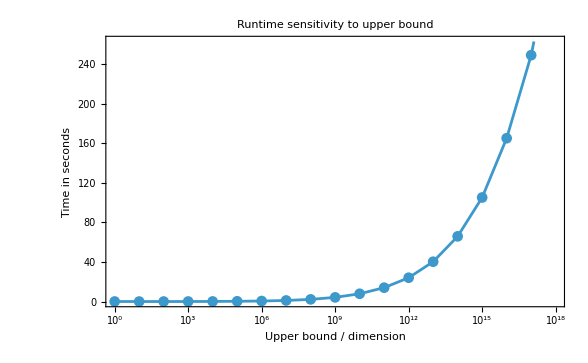

```mathematica
plotData=rows/. {Superscript[10,k_],numbers_,NumberForm[time_,___]}:>{k,time};
Plot2=ListLogPlot[plotData,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / dimension","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData),None}},PlotLabel->"Runtime sensitivity to upper bound"]
Plot2NonLog=ListPlot[plotData,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / dimension","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData),None}},PlotLabel->"Runtime sensitivity to upper bound"]
```

## 3 Digit Permutation Class Approach

```mathematica
maxdimension = 18;
```

```mathematica
digitVector[n_]:=Table[Count[IntegerDigits[n],d],{d,0,9}]
```

```mathematica
digitVectorsOfLength[digits_]:=FrobeniusSolve[ConstantArray[1,10],digits]
permutationClassVectorPowerSum[v_]:=Module[{digits},digits=Total[v];
Sum[v[[d+1]]*d^digits,{d,0,9}]]
```

```mathematica
returnNarcissisticPermutationRange[lower_,upper_]:=Module[{time,numbers,minDigits,maxDigits,vectors},minDigits=Max[1,IntegerLength[lower]];
maxDigits=IntegerLength[upper];
{time,numbers}=AbsoluteTiming[vectors=Join@@Table[digitVectorsOfLength[d],{d,minDigits,maxDigits}];
numbers=Table[Module[{value},value=permutationClassVectorPowerSum[v];
If[lower<=value<=upper&&digitVector[value]==v,value,Nothing]],{v,vectors}];
Sort[DeleteDuplicates[numbers]]];
{numbers,time}]
```

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticPermutationRange[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Table3 = Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

Upper bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.037300
10^1 | ; ; 23456789 | 0.001941
10^2 | ; ;  | 0.007671
10^3 | ; ; 153370371407 | 0.026185
10^4 | ; ; 163482089474 | 0.098129
10^5 | ; ; 547489272793084 | 0.249203
10^6 | ; ; 548834 | 0.512602
10^7 | ; ; 1741725421081898008179926315 | 1.076605
10^8 | ; ; 246780502467805188593477 | 2.183054
10^9 | ; ; 146511208472335975534494836912985153 | 4.200051
10^10 | ; ; 4679307774 | 7.848288
10^11 | ; ; 3216404965032164049651400283942254267829060344708635679493885506068269391657894204591914 | 14.011023
10^12 | ; ;  | 24.060938
10^13 | ; ;  | 40.222029
10^14 | ; ; 28116440335967 | 65.848590
10^15 | ; ;  | 105.119756
10^16 | ; ; 43382817693913704338281769391371 | 165.007447
10^17 | ; ; 218971425876120753564159420896413235875699062250035 | 248.930297
10^18 | ; ;  | 370.283081

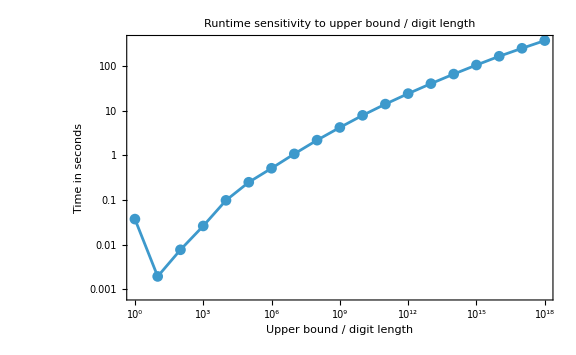

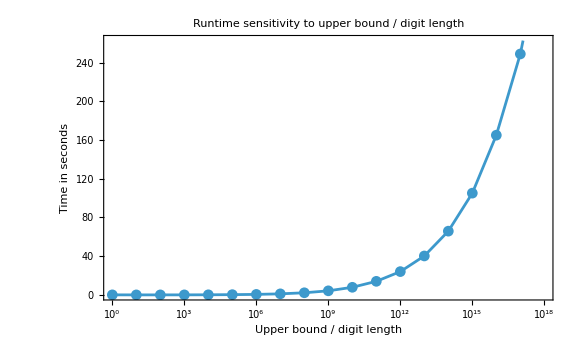

```mathematica
plotData3=Cases[rows,{Superscript[10,k_],_,NumberForm[time_,___]}:>{k,time}];
Plot3=ListLogPlot[plotData3,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / digit length","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData3),None}},PlotLabel->"Runtime sensitivity to upper bound / digit length",ImageSize->Large]
Plot3NonLog=ListPlot[plotData3,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / digit length","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData3),None}},PlotLabel->"Runtime sensitivity to upper bound / digit length",ImageSize->Large]
```

```mathematica
LaunchKernels[];

DistributeDefinitions[digitVector,digitVectorsOfLength,permutationClassVectorPowerSum]
```

{digitVector,digitVectorsOfLength,permutationClassVectorPowerSum}

```mathematica
returnNarcissisticPermutationRangeParallel[lower_,upper_]:=Module[{time,numbers,minDigits,maxDigits,vectors},If[$KernelCount==0,LaunchKernels[]];
DistributeDefinitions[digitVector,digitVectorsOfLength,permutationClassVectorPowerSum];
minDigits=Max[1,IntegerLength[lower]];
maxDigits=IntegerLength[upper];
{time,numbers}=AbsoluteTiming[vectors=Join@@Table[digitVectorsOfLength[d],{d,minDigits,maxDigits}];
numbers=ParallelTable[Module[{value},value=permutationClassVectorPowerSum[v];
If[lower<=value<=upper&&digitVector[value]==v,value,Nothing]],{v,vectors}];
Sort[DeleteDuplicates[numbers]]];
{numbers,time}]
```

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticPermutationRangeParallel[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Table4 = Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

Upper bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.022127
10^1 | ; ; 23456789 | 0.009778
10^2 | ; ;  | 0.017805
10^3 | ; ; 153370371407 | 0.046117
10^4 | ; ; 163482089474 | 0.208358
10^5 | ; ; 547489272793084 | 0.413190
10^6 | ; ; 548834 | 0.747108
10^7 | ; ; 1741725421081898008179926315 | 1.338130
10^8 | ; ; 246780502467805188593477 | 2.269051
10^9 | ; ; 146511208472335975534494836912985153 | 4.124852
10^10 | ; ; 4679307774 | 7.438569
10^11 | ; ; 3216404965032164049651400283942254267829060344708635679493885506068269391657894204591914 | 13.193473
10^12 | ; ;  | 22.925036
10^13 | ; ;  | 38.883356
10^14 | ; ; 28116440335967 | 64.934582
10^15 | ; ;  | 106.783557

```mathematica
plotData4=Cases[rows,{Superscript[10,k_],_,NumberForm[time_,___]}:>{k,time}];
Plot4=ListLogPlot[plotData3,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / digit length","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData3),None}},PlotLabel->"Runtime sensitivity to upper bound / digit length",ImageSize->Large]
Plot4NonLog=ListPlot[plotData3,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Upper bound / digit length","Time in seconds"},FrameTicks->{{Automatic,None},{({#[[1]],Superscript[10,#[[1]]]}&/@plotData3),None}},PlotLabel->"Runtime sensitivity to upper bound / digit length",ImageSize->Large]
```

-Graphics-

-Graphics-

## 4 Sensitivity Analysis

### 4.1 Sensitivity to Search Dimensions

```mathematica
Clear[candidateCount,digitClassCount]

candidateCount[d_]:=If[d==1,10,9*10^(d-1)]

digitClassCount[d_]:=Binomial[d+9,9]

complexityRows=Table[{d,candidateCount[d],digitClassCount[d],NumberForm[N[candidateCount[d]/digitClassCount[d]],{Infinity,2}]},{d,1,maxdimension}];

Table5 = Grid[Prepend[complexityRows,{"Digit length","Brute force candidates","Digit classes","Reduction factor"}],Frame->All]
```

Digit length | Brute force candidates | Digit classes | Reduction factor
1 | 10 | 10 | 1.00
2 | 90 | 55 | 1.64
3 | 900 | 220 | 4.09
4 | 9000 | 715 | 12.59
5 | 90000 | 2002 | 44.96
6 | 900000 | 5005 | 179.82
7 | 9000000 | 11440 | 786.71
8 | 90000000 | 24310 | 3702.18
9 | 900000000 | 48620 | 18510.90
10 | 9000000000 | 92378 | 97425.79
11 | 90000000000 | 167960 | 535841.87
12 | 900000000000 | 293930 | 3.06×10^6
13 | 9000000000000 | 497420 | 1.81×10^7
14 | 90000000000000 | 817190 | 1.10×10^8
15 | 900000000000000 | 1307504 | 6.88×10^8
16 | 9000000000000000 | 2042975 | 4.41×10^9
17 | 90000000000000000 | 3124550 | 2.88×10^10
18 | 900000000000000000 | 4686825 | 1.92×10^11

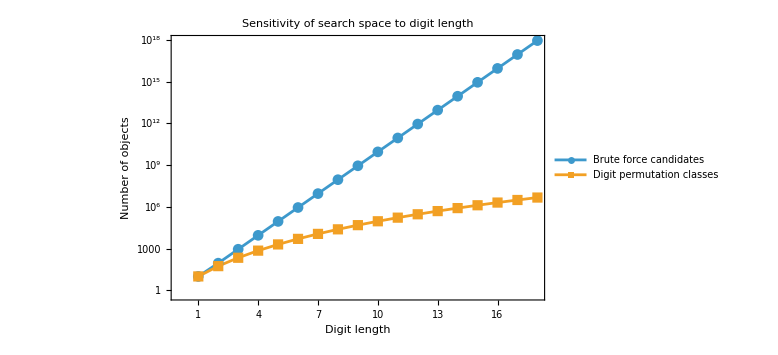

-Graphics-

```mathematica
Plot5=ListLogPlot[{complexityRows[[All,{1,2}]],complexityRows[[All,{1,3}]]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Digit length","Number of objects"},FrameTicks->{{Automatic,None},{Range[1,maxdimension],None}},PlotLabel->"Sensitivity of search space to digit length",PlotLegends->Placed[{"Brute force candidates","Digit permutation classes"},Below],ImageSize->Large]
Plot5NonLog=ListPlot[{complexityRows[[All,{1,2}]],complexityRows[[All,{1,3}]]},Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Digit length","Number of objects"},FrameTicks->{{Automatic,None},{Range[1,maxdimension],None}},PlotLabel->"Sensitivity of search space to digit length",PlotLegends->Placed[{"Brute force candidates","Digit permutation classes"},Below],ImageSize->Large]
```

### 4.2 Sensitivity to Algorithmic Approach

```mathematica
Clear[measureRuntime,formatRuntimeRow]

measureRuntime[name_,func_,d_Integer,repetitions_:3,timeLimit_:600]:=Module[{lower,upper,runs,successfulRuns,times,nums,t},{lower,upper}=dimensionRange[d];
runs=Table[TimeConstrained[{nums,t}=func[lower,upper];
{nums,t},timeLimit,$Failed],{repetitions}];
successfulRuns=DeleteCases[runs,$Failed];
If[successfulRuns==={},{name,d,lower,upper,0,Missing["Timeout"],Missing["NotAvailable"],Missing["NotAvailable"]},times=successfulRuns[[All,2]];
{name,d,lower,upper,Length[successfulRuns],Mean[times],If[Length[times]>1,StandardDeviation[times],0],Length[First[successfulRuns][[1]]]}]]

formatRuntimeRow[row_]:=Module[{name,d,lower,upper,completed,mean,sd,found},{name,d,lower,upper,completed,mean,sd,found}=row;
{name,d,Row[{lower," - ",upper}],completed,If[Head[mean]===Missing,"timeout",NumberForm[mean,{Infinity,6}]],If[Head[sd]===Missing,"-",NumberForm[sd,{Infinity,6}]],If[Head[found]===Missing,"-",found]}]
```

```mathematica
settings={{"Brute force",returnNarcissisticRange,Range[1,7]},{"Parallel brute force",returnNarcissisticParallelRange,Range[1,8]},{"Digit permutation class",returnNarcissisticPermutationRange,Range[1,18]},{"Parallel digit permutation class",returnNarcissisticPermutationRangeParallel,Range[1,18]}};

repetitions=3;

runtimeRows=Flatten[Table[Table[measureRuntime[setting[[1]],setting[[2]],d,repetitions,600],{d,setting[[3]]}],{setting,settings}],1];

Table6 = Grid[Prepend[formatRuntimeRow/@runtimeRows,{"Method","Digits","Range","Completed runs","Mean time","Std. dev.","Numbers found"}],Frame->All]
```

$Aborted

Method | Digits | Range | Completed runs | Mean time | Std. dev. | Numbers found
Brute force | 1 | 0 - 9 | 1 | 0.000086 | 0 | 10
Brute force | 2 | 10 - 99 | 1 | 0.000590 | 0 | 0
Brute force | 3 | 100 - 999 | 1 | 0.007313 | 0 | 4
Brute force | 4 | 1000 - 9999 | 1 | 0.086401 | 0 | 3
Brute force | 5 | 10000 - 99999 | 1 | 1.057389 | 0 | 3
Brute force | 6 | 100000 - 999999 | 1 | 11.339210 | 0 | 1
Brute force | 7 | 1000000 - 9999999 | 1 | 125.101505 | 0 | 4
Parallel brute force | 1 | 0 - 9 | 1 | 0.020837 | 0 | 10
Parallel brute force | 2 | 10 - 99 | 1 | 0.004625 | 0 | 0
Parallel brute force | 3 | 100 - 999 | 1 | 0.007928 | 0 | 4
Parallel brute force | 4 | 1000 - 9999 | 1 | 0.030714 | 0 | 3
Parallel brute force | 5 | 10000 - 99999 | 1 | 0.204515 | 0 | 3
Parallel brute force | 6 | 100000 - 999999 | 1 | 2.374786 | 0 | 1
Parallel brute force | 7 | 1000000 - 9999999 | 1 | 28.359877 | 0 | 4
Parallel brute force | 8 | 10000000 - 99999999 | 1 | 321.166371 | 0 | 3
Digit permutation class | 1 | 0 - 9 | 1 | 0.000686 | 0 | 10
Digit permutation class | 2 | 10 - 99 | 1 | 0.002077 | 0 | 0
Digit permutation class | 3 | 100 - 999 | 1 | 0.007996 | 0 | 4
Digit permutation class | 4 | 1000 - 9999 | 1 | 0.025878 | 0 | 3
Digit permutation class | 5 | 10000 - 99999 | 1 | 0.107266 | 0 | 3
Digit permutation class | 6 | 100000 - 999999 | 1 | 0.241893 | 0 | 1
Digit permutation class | 7 | 1000000 - 9999999 | 1 | 0.474049 | 0 | 4
Digit permutation class | 8 | 10000000 - 99999999 | 1 | 0.955957 | 0 | 3
Digit permutation class | 9 | 100000000 - 999999999 | 1 | 1.850746 | 0 | 4
Digit permutation class | 10 | 1000000000 - 9999999999 | 1 | 3.500084 | 0 | 1
Digit permutation class | 11 | 10000000000 - 99999999999 | 1 | 6.295734 | 0 | 8
Digit permutation class | 12 | 100000000000 - 999999999999 | 1 | 10.949010 | 0 | 0
Digit permutation class | 13 | 1000000000000 - 9999999999999 | 1 | 18.553947 | 0 | 0
Digit permutation class | 14 | 10000000000000 - 99999999999999 | 1 | 30.646091 | 0 | 1
Digit permutation class | 15 | 100000000000000 - 999999999999999 | 1 | 49.290231 | 0 | 0
Digit permutation class | 16 | 1000000000000000 - 9999999999999999 | 1 | 84.245402 | 0 | 2
Digit permutation class | 17 | 10000000000000000 - 99999999999999999 | 1 | 121.511005 | 0 | 3
Digit permutation class | 18 | 100000000000000000 - 999999999999999999 | 1 | 181.418070 | 0 | 0
Parallel digit permutation class | 1 | 0 - 9 | 1 | 0.005167 | 0 | 10
Parallel digit permutation class | 2 | 10 - 99 | 1 | 0.008191 | 0 | 0
Parallel digit permutation class | 3 | 100 - 999 | 1 | 0.015426 | 0 | 4
Parallel digit permutation class | 4 | 1000 - 9999 | 1 | 0.027969 | 0 | 3
Parallel digit permutation class | 5 | 10000 - 99999 | 1 | 0.209746 | 0 | 3
Parallel digit permutation class | 6 | 100000 - 999999 | 1 | 0.298001 | 0 | 1
Parallel digit permutation class | 7 | 1000000 - 9999999 | 1 | 0.520012 | 0 | 4
Parallel digit permutation class | 8 | 10000000 - 99999999 | 1 | 0.981736 | 0 | 3
Parallel digit permutation class | 9 | 100000000 - 999999999 | 1 | 1.647059 | 0 | 4
Parallel digit permutation class | 10 | 1000000000 - 9999999999 | 1 | 2.952005 | 0 | 1
Parallel digit permutation class | 11 | 10000000000 - 99999999999 | 1 | 5.028095 | 0 | 8
Parallel digit permutation class | 12 | 100000000000 - 999999999999 | 1 | 8.657483 | 0 | 0
Parallel digit permutation class | 13 | 1000000000000 - 9999999999999 | 1 | 15.079858 | 0 | 0
Parallel digit permutation class | 14 | 10000000000000 - 99999999999999 | 1 | 24.962729 | 0 | 1
Parallel digit permutation class | 15 | 100000000000000 - 999999999999999 | 1 | 40.707267 | 0 | 0
Parallel digit permutation class | 16 | 1000000000000000 - 9999999999999999 | 1 | 65.681217 | 0 | 2
Parallel digit permutation class | 17 | 10000000000000000 - 99999999999999999 | 1 | 103.157502 | 0 | 3
Parallel digit permutation class | 18 | 100000000000000000 - 999999999999999999 | 1 | 167.621830 | 0 | 0

```mathematica
Plot6=ListLogPlot[runtimePlotData,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Digit length","Mean runtime in seconds"},FrameTicks->{{Automatic,None},{Range[1,maxdimension],None}},PlotLegends->Placed[settings[[All,1]],Below],PlotLabel->"Runtime sensitivity by digit length",GridLines->Automatic,ImageSize->Large,PlotRange->All]
Plot6NonLog=ListPlot[runtimePlotData,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Digit length","Mean runtime in seconds"},FrameTicks->{{Automatic,None},{Range[1,maxdimension],None}},PlotLegends->Placed[settings[[All,1]],Below],PlotLabel->"Runtime sensitivity by digit length",GridLines->Automatic,ImageSize->Large,PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics-

### 4.3 Sensitivity to Parallelization

```mathematica
Clear[kernelSensitivityRows]

testDimension=16;
kernelCounts=Range[1,Min[6,$ProcessorCount]];

kernelSensitivityRows=Table[CloseKernels[];
LaunchKernels[kernels];
DistributeDefinitions[returnNarcissisticPermutationRangeParallel,dimensionRange];
returnNarcissisticPermutationRangeParallel@@dimensionRange[3];
{numbers,time}=AbsoluteTiming[returnNarcissisticPermutationRangeParallel@@dimensionRange[testDimension]][[{2,1}]];
{kernels,testDimension,time,Length[numbers]},{kernels,kernelCounts}];

CloseKernels[];

Table7 =  Grid[Prepend[kernelSensitivityRows,{"Kernels","Digit length","Time in seconds","Numbers found"}],Frame->All]
```

Set::write: Tag Times in 7 Table is Protected.

Kernels | Digit length | Time in seconds | Numbers found
1 | 16 | 121.401 | 2
2 | 16 | 83.4399 | 2
3 | 16 | 72.0325 | 2
4 | 16 | 67.7921 | 2
5 | 16 | 66.6319 | 2
6 | 16 | 65.9792 | 2

```mathematica
kernelPlotData=kernelSensitivityRows[[All,{1,3}]];

Plot7=ListLinePlot[kernelPlotData,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Number of kernels","Time in seconds"},FrameTicks->{{Automatic,None},{kernelCounts,None}},PlotLabel->"Runtime sensitivity to number of kernels",GridLines->Automatic,ImageSize->Large,PlotRange->All]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLinePlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

ListLinePlot[Symbol[],Joined→True,PlotMarkers→Automatic,Frame→True,Axes→False,FrameLabel→{Number of kernels,Time in seconds},FrameTicks→{{Automatic,None},{kernelCounts,None}},PlotLabel→Runtime sensitivity to number of kernels,GridLines→Automatic,ImageSize→Large,PlotRange→All]